#### Step H: Histogram plots (version 2)

```mathematica
2*2
```

4

```mathematica
filenameVolumeBase="FR96D3_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/"
concFRD3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_374_374_492.h5",{"Datasets","concFR"}];
Dimensions[concFRD3]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/

{492,374,374}

```mathematica
filenameVolumeBase="FR96D1_";
concFRD1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRD1]
```

{309,566,374}

```mathematica
filenameVolumeBase="FR96C1_";
concFRC1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRC1]
```

{250,400,560}

```mathematica
filenameVolumeBase="FR96B1_";
concFRB1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRB1]
```

{200,350,500}

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concFRD3],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRD3 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRD3]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concFRD1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRD1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRD1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRC1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRC1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRC1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRB1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRB1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRB1]
```

{54.0768,Null}

68256581

1000000

{54.1638,Null}

60108823

1000000

{46.177,Null}

51173252

1000000

{29.3545,Null}

32253739

1000000

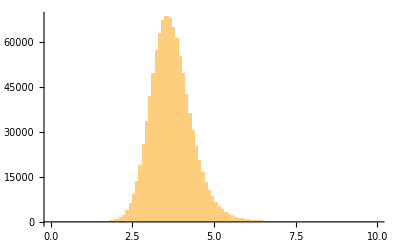

3.70961

0.675987

```mathematica
Histogram[concFRD3,{0.0,10,0.1}]
Mean[concFRD3]
StandardDeviation[concFRD3]
```

```mathematica
list =HistogramList[concFRD3,{0.0,100,0.1}];
threshold=5.1;
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionBFRinlumps = 100*volPercentNumerator/volPercentDenominator
```

52

155243.

3.70962×10^6

4.18487

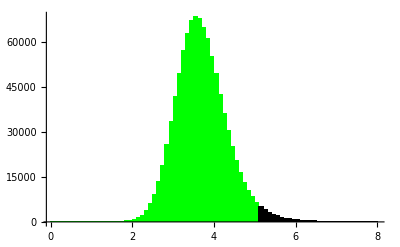

```mathematica
listBelowThreshold = Histogram[Select[concFRD3,#<threshold &],{0.0,8,0.1},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concFRD3,#>=threshold &],{0,8,0.1},ChartStyle->Directive[Black,EdgeForm[]]];
gFRD3=Show[{listBelowThreshold,listAboveThreshold}]
```

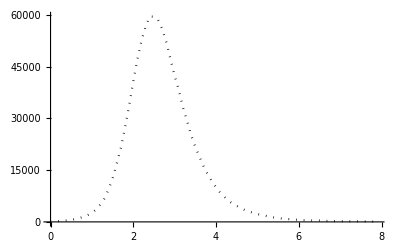
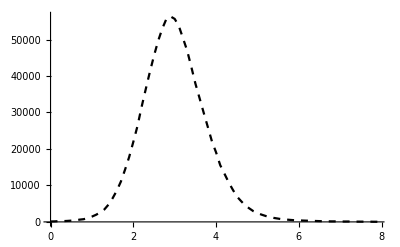
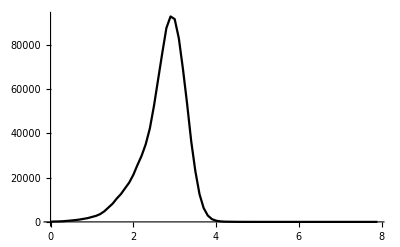

```mathematica
data =HistogramList[concFRB1,{0,8,0.1}];
gFRB1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]];
data =HistogramList[concFRC1,{0,8,0.1}];
gFRC1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]];
data =HistogramList[concFRD1,{0,8,0.1}];
gFRD1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]];
{gFRB1,gFRC1,gFRD1}
```

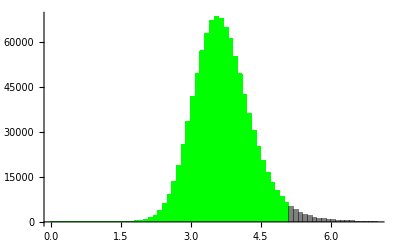

```mathematica
gHistD3=Histogram[{
Select[concFRD3,#<threshold &],
Select[concFRD3,#>=threshold &]},{0,7,.1},
ChartStyle->{ Directive[Green,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

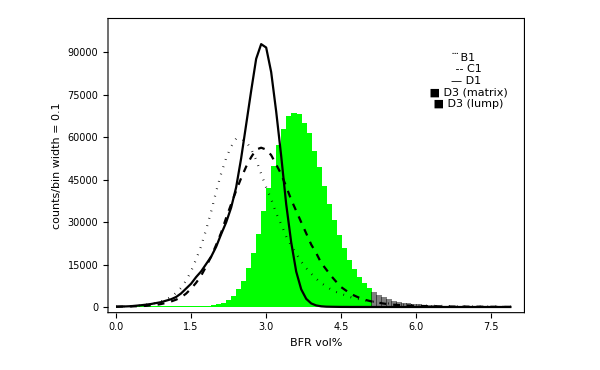

```mathematica
Show[{gHistD3,gFRD1,gFRB1,gFRC1},PlotRange->{{0,8},{0,100000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"counts/bin width = 0.1",""},{"BFR vol%",""}},
Epilog->Style[Text[Framed[" ⃛ B1\n -- C1\n— D1\n ■ D3 (matrix)\n ■ D3 (lump)"],{7.0,80000}],16,TextAlignment->Right]]
```